```mathematica
(E^(-ζ^2)-E^(-a^2))/(ζ+a)
Series[%,{ζ,0,1}]//Normal//Simplify
```

(-ⅇ^(-a^2)+ⅇ^(-ζ^2))/(a+ζ)

(ⅇ^(-a^2) (-1+ⅇ^(a^2)) (a-ζ))/a^2

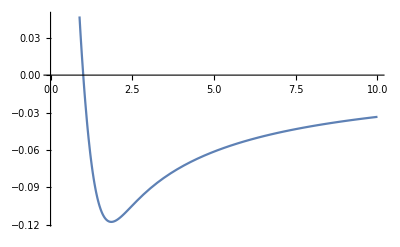

```mathematica
Plot[(E^(-ζ^2)-E^(-a^2))/(ζ+a)/.a->1,{ζ,0,10}]
```

```mathematica
Integrate[(E^(-ζ^2)-E^(-a^2))/(ζ+a),ζ]
```

∫(-ⅇ^(-a^2)+ⅇ^(-ζ^2))/(a+ζ)ⅆζ

```mathematica
1/(mi^2 Sqrt[2 π] βD^2) nF (mi βD)^(3/2) (2 mi vesc βD+E^(1/2 mi vesc^2 βD) Sqrt[2 π] Sqrt[mi βD]-E^(1/2 mi vesc^2 βD) Sqrt[mi] Sqrt[2 π] Sqrt[βD] Erf[(Sqrt[mi] vesc Sqrt[βD])/Sqrt[2]])/.Solve[1/2 mi vesc^2 βD== x,vesc][[2]]//Simplify//PowerExpand
```

nF (ⅇ^x+(2 √x)/(√π)-ⅇ^x Erf[√x])

```mathematica
Series[(ⅇ^x-(2 √x)/(√π)+ⅇ^x Erf[√x]),{x,0,1}]
Series[(ⅇ^x+(2 √x)/(√π)-ⅇ^x Erf[√x]),{x,0,1}]
```

1+x+O[x]^(3/2)

1+x+O[x]^(3/2)

```mathematica
4 √(1/π)Integrate[v^2 E^(-v^2 + x^2),{v,x,∞}]
```

(2 x+ⅇ^(x^2) √π Erfc[x])/(√π)

```mathematica
Solve[1/2 mi vesc^2 βD== x,vesc][[2]]
```

{vesc→(√2 √x)/(√mi √βD)}

```mathematica
2(1+ -1/(1+z/a))(1-E^(-a^2))- (E^(-z^2)+E^(-a^2))Log[(a-z)/(a+z)]
Series[%,{z,∞,1}]
```

2 (1-ⅇ^(-a^2)) (1-1/(1+z/a))-(ⅇ^(-a^2)+ⅇ^(-z^2)) Log[(a-z)/(a+z)]

(ⅇ^(-a^2) (-2+2 ⅇ^(a^2)-ⅈ π)-(2 (a ⅇ^(-a^2) (-2+ⅇ^(a^2))))/z+O[1/z]^2)+ⅇ^(-z^2+O[1/z]^2) (-ⅈ π+(2 a)/z+O[1/z]^2)

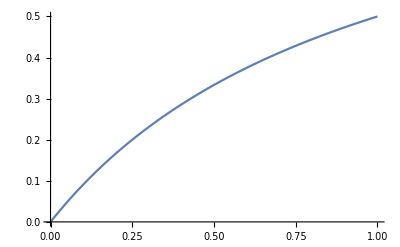

```mathematica
Plot[1+-1/(1+x),{x,0,1}]
```

```mathematica
Log[(a-z)/(a+z)]
Series[%,{z,0,1}]
```

Log[(a-z)/(a+z)]

-(2 z)/a+O[z]^2

(2 (1-ⅇ^(-a^2)) z)/a-(ⅇ^(-a^2)+ⅇ^(-z^2)) Log[(a-z)/(a+z)]

-((1+ⅇ^(-z^2)) Log[(a-z)/(a+z)])

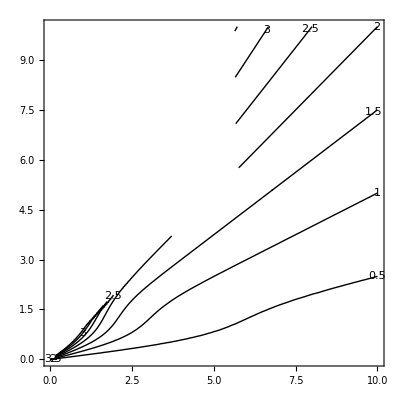

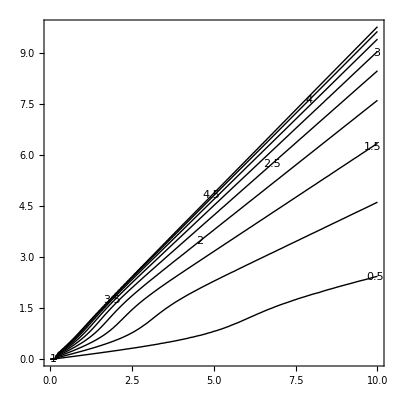

```mathematica
2(z/a)(1-E^(-a^2))- (E^(-z^2)+E^(-a^2))Log[(a-z)/(a+z)]
-Log[(a-z)/(a+z)]((1-E^(-a^2))+ (E^(-z^2)+E^(-a^2)))//Simplify
ContourPlot[%%,{a,0,10},{z,0,10},ContourShading->None,ContourLabels->True,PlotRange->All]
ContourPlot[%%,{a,0,10},{z,0,10},ContourShading->None,ContourLabels->True,PlotRange->All]
```